## Equilibrium calculation

```mathematica
A[u_,α_,γ_]:=(u/(1-u)+1-γ)/(α γ);
equilibrium[r_,β_,u_,α_,γ_]:=1/(((r+1)/(A[u,α,γ] (r-1)+r)-1)^(1/β)+1);
```

```mathematica
q2=3;q1=2;β=.;u=0;α=0.8;
Manipulate[eq2a=Plot[equilibrium[q2/q1,β,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.01]],Frame->True,AspectRatio->1],{β,0.001,2}]
```

## Figr1

```mathematica
raw2mr1=Import[NotebookDirectory[]<>"2m_r1.csv","CSV"];
```

```mathematica
heat2a=ListDensityPlot[raw2mr1⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

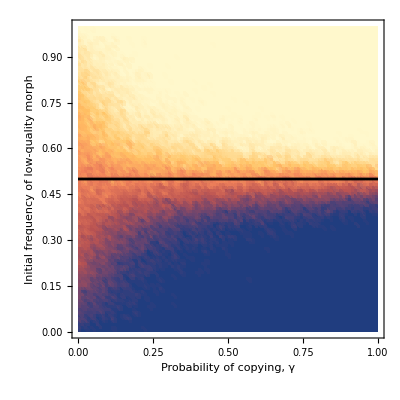

```mathematica
Show[heat2a,Plot[equilibrium[1/1,2,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

## Figr1pt5

```mathematica
rawr1pt5a=Import[NotebookDirectory[]<>"2m_r1.5.csv","CSV"];
```

```mathematica
heat2b=ListDensityPlot[rawr1pt5a⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Normalised fixation time",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

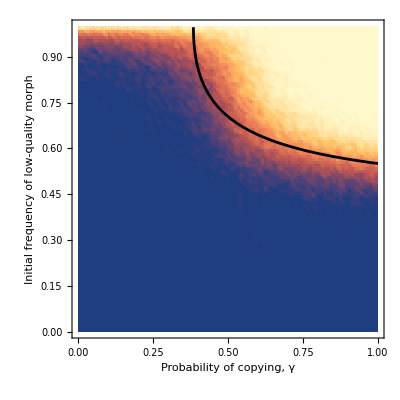

```mathematica
Show[heat2b,Plot[equilibrium[1.5/1,2,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

```mathematica
rawr1pt5b=Import[NotebookDirectory[]<>"2m_r1.5_6_4.csv","CSV"];
```

```mathematica
heat2bb=ListDensityPlot[rawr1pt5b⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Normalised fixation time",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

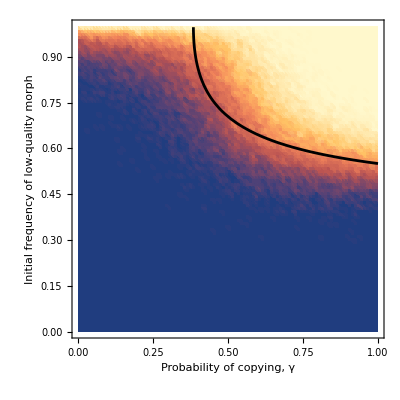

```mathematica
Show[heat2bb,Plot[equilibrium[1.5/1,2,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

## Figr1pt8

```mathematica
raw2mr1pt8=Import[NotebookDirectory[]<>"2m_r1.8.csv","CSV"];
```

```mathematica
heat2c=ListDensityPlot[raw2mr1pt8⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

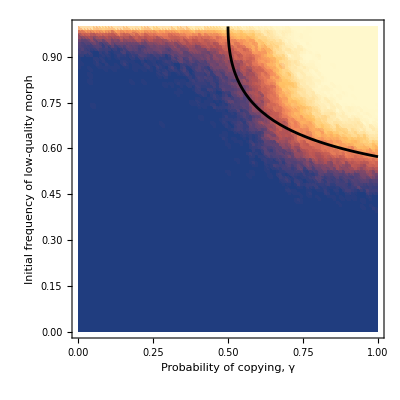

```mathematica
Show[heat2c,Plot[equilibrium[1.8/1,2,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

## Figr4pt2

```mathematica
raw2mr4pt2=Import[NotebookDirectory[]<>"2m_r4.2.csv","CSV"];
```

```mathematica
heat2d=ListDensityPlot[raw2mr4pt2⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}];
```

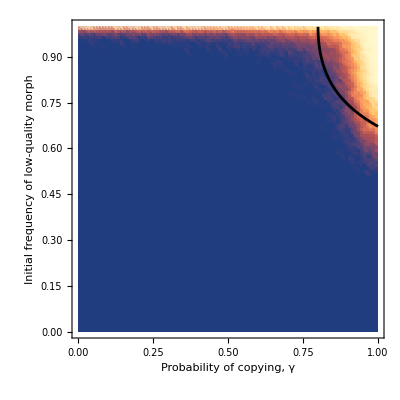

```mathematica
Show[heat2d,Plot[equilibrium[4.2/1,2,u,α,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```